```mathematica
Remove["Global`*"]
```

```mathematica
h = {{0,ϵ*/2,0},{ϵ/2,δ,Sqrt[2]ϵ*/2},{0,Sqrt[2]ϵ/2,α+2δ}}
```

{{0,Conjugate[ϵ]/2,0},{ϵ/2,δ,Conjugate[ϵ]/(√2)},{0,ϵ/(√2),α+2 δ}}

```mathematica
h // MatrixForm
```

(0 | Conjugate[ϵ]/2 | 0
ϵ/2 | δ | Conjugate[ϵ]/(√2)
0 | ϵ/(√2) | α+2 δ)

```mathematica
Clear[gaussianPulse]
```

```mathematica
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0]<(w-Sqrt[2π dt])/2:=1
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0]≥(w-Sqrt[2π dt])/2&& t > t0:=Exp[-(t-t0-(w-Sqrt[2π dt])/2)^2/dt/2]
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0]≥(w-Sqrt[2π dt])/2&& t <= t0:=Exp[-(t-t0+(w-Sqrt[2π dt])/2)^2/dt/2]
```

```mathematica
Assuming[dt>0,NIntegrate[gaussianPulse[t,100,100,5],{t,-Infinity,Infinity}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {143.492}. NIntegrate obtained 100.005 and 0.0527466 for the integral and error estimates.

100.005

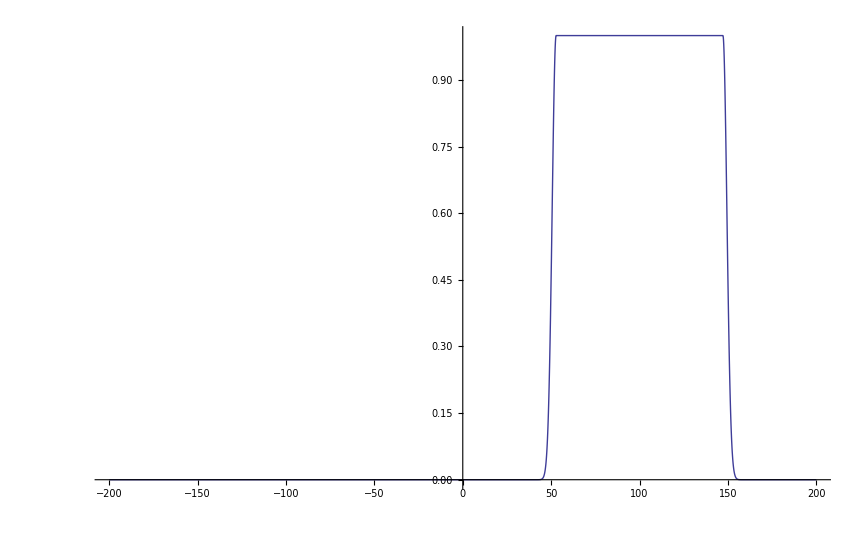

```mathematica
Plot[gaussianPulse[t,100,100,5],{t,-200,200}]
```

```mathematica
heff = h /. {δ->0.,α->-.240,ϵ->π 0.1 *gaussianPulse[t,10,20,5]};
heff //MatrixForm
psisolution = NDSolve[{psi'[t] == -I heff. psi[t],psi[0]=={1,0,0}},psi,{t,0,100}]
```

(0 | 0.15708 Conjugate[gaussianPulse[t,10,20,5]] | 0
0.15708 gaussianPulse[t,10,20,5] | 0. | 0.222144 Conjugate[gaussianPulse[t,10,20,5]]
0 | 0.222144 gaussianPulse[t,10,20,5] | -0.24)

{{psi→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
drive[ϕ_,t_]:= π 0.1 *(gaussianPulse[t,10,5.,1.]+Exp[I ϕ] *gaussianPulse[t,20,5.,1.])
hϕ[t_,ϕ_]:= Block[{δ=-0.16,α=-.240*2,ϵ=drive[ϕ,t]},h /. {δ->δ,α->α,ϵ->ϵ,ϕ->ϕ}] ;
phisolution[ϕ_] := NDSolve[{psi'[t] == -I hϕ[t,ϕ]. psi[t],psi[0]=={1,0,0}},psi,{t,0,60}];
phisequence[ϕ_]:=1-Evaluate[Abs[psi[60.0] /. phisolution[ϕ] ] [[1]]][[1]]^2;
```

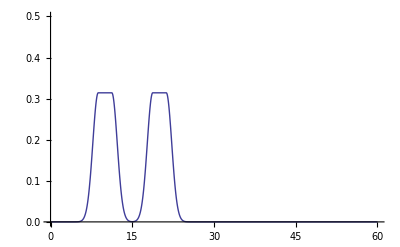

```mathematica
Plot[drive[0,t],{t,0,60},PlotRange->{0,0.5}]
```

```mathematica
phases =Range[0,4π,π/8];
values = Map[phisequence[#]&,phases];
```

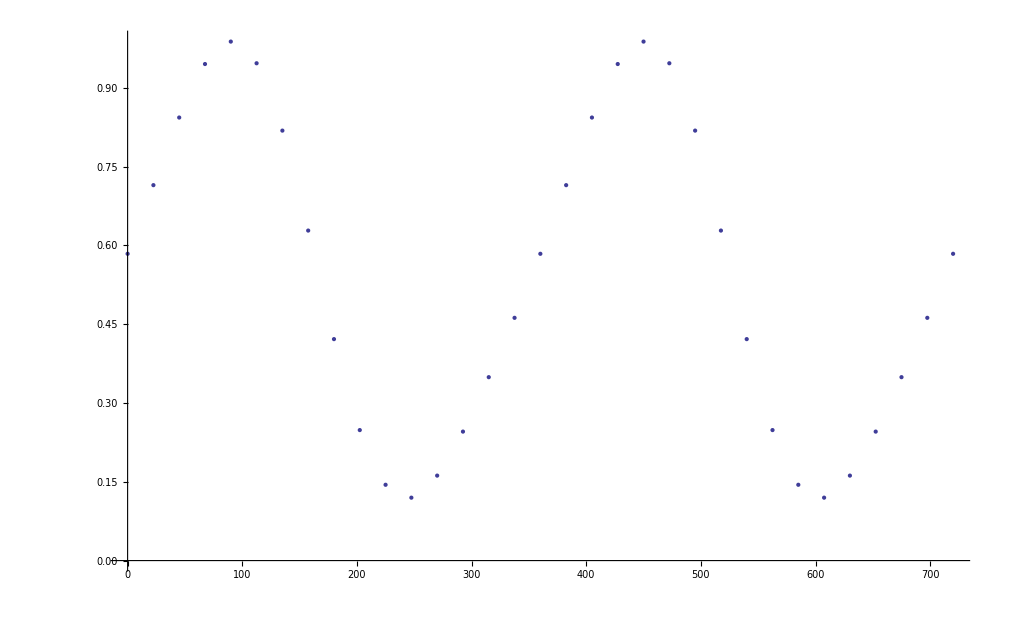

```mathematica
ListPlot[Map[{phases[[#]]*180./π,values[[#]]}&,Range[1,Length[phases]]]]
```

{{psi→InterpolatingFunction[{{0.,100.}},<>]}}

{InterpolatingFunction[{{0.,100.}},<>][t]}

{InterpolatingFunction[{{0.,100.}},<>][t]}

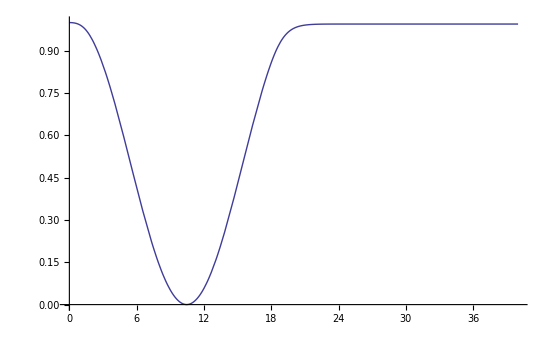

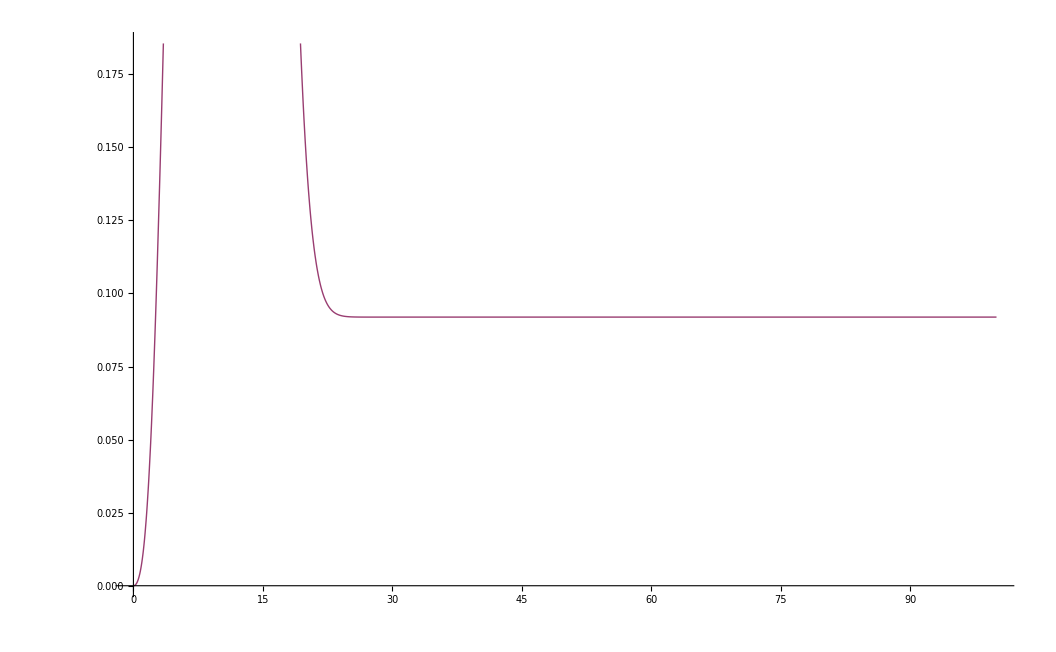

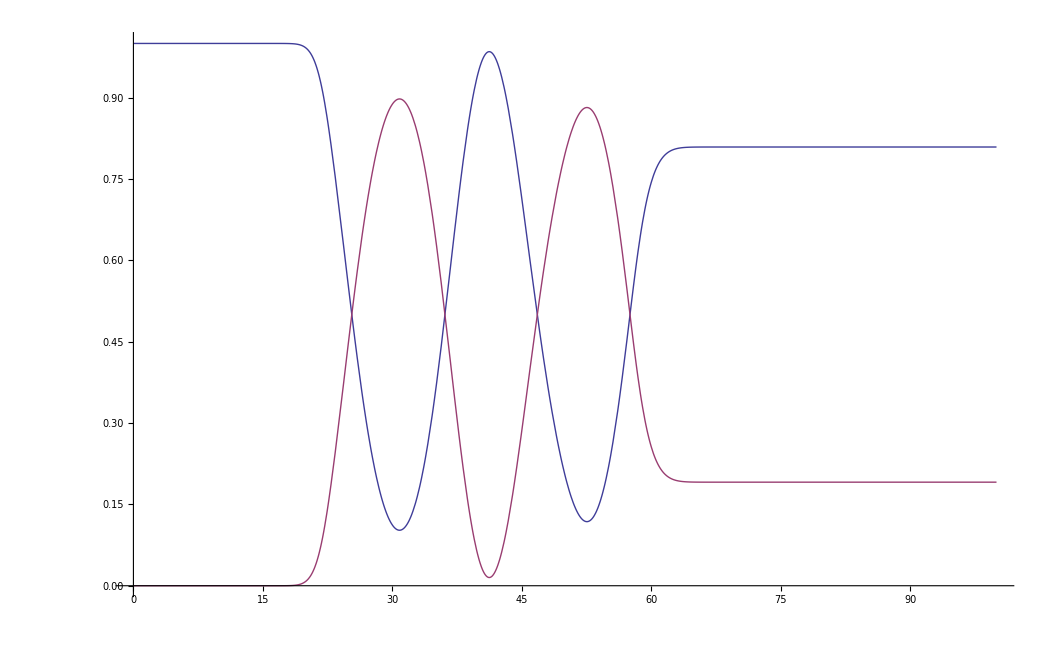

```mathematica
myphisolution = phisolution[0.4]
psi[t] /. myphisolution
psi[t] /. psisolution
Plot[{Evaluate[Abs[psi[t] /. myphisolution ][[1]]][[1]]^2},{t,0,40},PlotRange->Full]
```

```mathematica
I*h.{1,1,0} /. {ϵ->0,δ->1.,α->1./25.}
```

{0,0.+1. ⅈ,0}

```mathematica
NIntegrate[{0.1,I,0.1},{t,0,10}]
```

{1.,0.+10. ⅈ,1.}

```mathematica
ψ
```

ψ

```mathematica
{ψ'[t] == -I heff. ψ[t],ψ[0]={0,1,0}}
```

{ψ'[t]==-ⅈ {{0,0.01,0},{0.01,1,0.0141421},{0,0.0141421,1}}.ψ[t],{0,1,0}}

```mathematica
MatrixExp[{{0,a*t},{-a*t,0}}] // MatrixForm
```

(Cos[a t] | Sin[a t]
-Sin[a t] | Cos[a t])

```mathematica
heff2 = {{0, π Ωr  },{ π  Ωr,0}} /. {Ωr->0.5}
heff2 //MatrixForm
psisolution2 = NDSolve[{psi'[t] == -I heff2. psi[t],psi[0]=={0,1}},psi,{t,0,50}]
```

{{0,1.5708},{1.5708,0}}

(0 | 1.5708
1.5708 | 0)

{{psi→InterpolatingFunction[{{0.,50.}},<>]}}

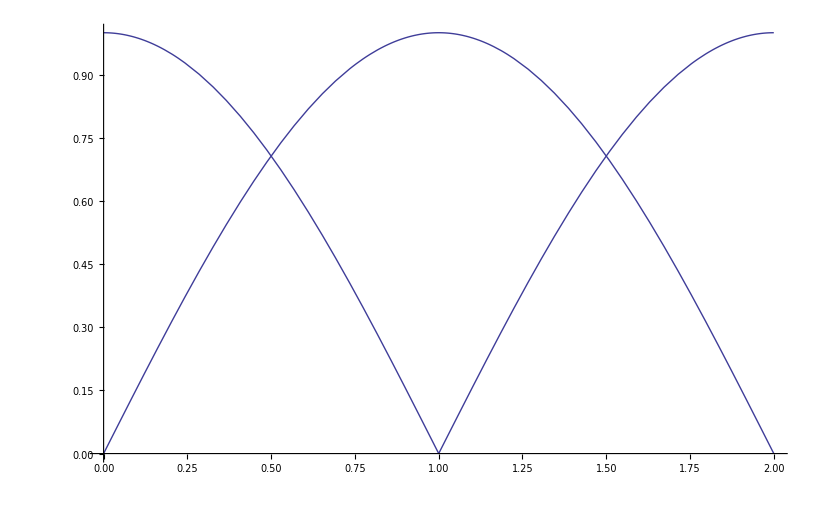

```mathematica
Plot[Abs[Evaluate[psi[t] /. psisolution2 ][[1]]],{t,0,2}]
```

```mathematica
Eigenvalues[heff]
```

{-0.286551,0.0988276,-0.0522771}

```mathematica
Eigenvectors[heff]
```

{{0.105353,-0.384377,0.917145},{0.602639,0.758309,0.248583},{-0.791029,0.526519,0.311531}}

```mathematica
Eigenvalues[heff /.{t->10.0}]
```

{-0.390674,0.219675,-0.0690012}

```mathematica
evs = Eigenvalues[h /. {ϵ->0.1,δ->0,α->0}]
```

{-0.0866025,0.0866025,3.43766×10^-18}